```mathematica
SetDirectory[NotebookDirectory[]];
```

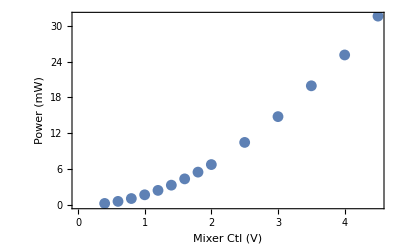

```mathematica
data=Import["MixerV_PowermW.csv"]//Rest;
ListPlot[data,Frame->True,FrameLabel->{"Mixer Ctl (V)", "Power (mW)"}]
```

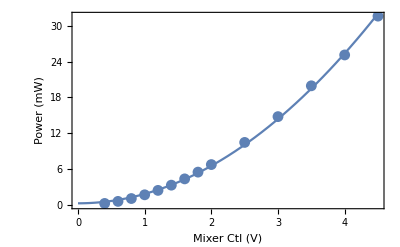

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.274447 | 0.107029 | 2.56423 | 0.0248077
x^2 | 1.56872 | 0.0128139 | 122.423 | 5.91683×10^-20

```mathematica
(*model =a+b x+c x^2*)
model=LinearModelFit[data,{x^2},x];
Show[ListPlot[data,Frame->True,FrameLabel->{"Mixer Ctl (V)", "Power (mW)"}],Plot[model[x],{x,0,5}]]
model["ParameterTable"]
```

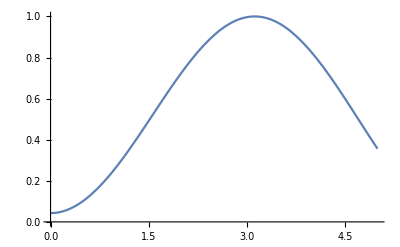

```mathematica
Plot[Sin[√model[x]]^2,{x,0,5}]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.235932 | 0.00697137 | -33.843 | 7.88556×10^-15
x | 0.935055 | 0.00813849 | 114.893 | 3.13977×10^-22

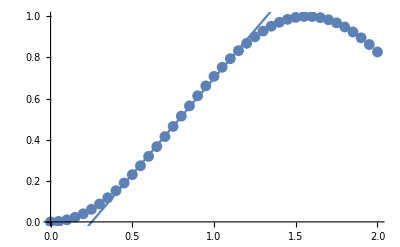

```mathematica
dd=Table[{x,Sin[x]^2},{x,0,2,.05}];
dm=LinearModelFit[dd[[10;;25]],x,x];
dm["ParameterTable"]
Show[ListPlot[dd],Plot[dm[x],{x,0,1.5}]]
```

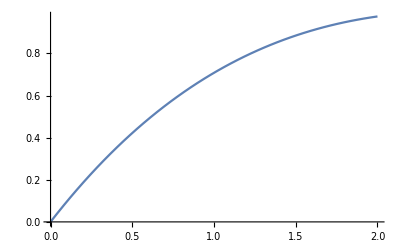

```mathematica
Plot[Sin[√x]^2,{x,0,2}]
```

```mathematica
p=TransferFunctionModel[{{k}},s];
i=TransferFunctionModel[{{k/(τ s)}},s];
PI=SystemsModelParallelConnect[p,i];
aom=TransferFunctionModel[{{A }},s];
out=SystemsModelSeriesConnect[PI,aom];
pd=TransferFunctionModel[{{Pd SystemsModelDelay[Δ]}},s];
ol=SystemsModelSeriesConnect[out,pd];
cl=SystemsModelFeedbackConnect[ol]
```

(A Pd (k+k τ s) Δ)/(τ s+A k Pd (1+τ s) Δ)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11$CellContext`A$CellContext`s1FalseFalseFalseAutomaticNoneNoneAutomatic

```mathematica
Manipulate[Block[{cltmp},
cltmp=ol/.{A->A0,k->k0,τ->τ0,Pd->pd0,Δ->Δ0};

{BodePlot[cltmp,StabilityMargins->True],GainPhaseMargins[cltmp]}],{A0,0.1,1},{k0,0.1,1},{τ0,0.1,1},{pd0,0.1,1},{Δ0,0,1}]
```

```mathematica
SystemsModelParallelConnect[TransferFunctionModel[{{k/(τ s)}},s],TransferFunctionModel[{{k}},s]]
```

(k+k τ s)/(τ s)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11$CellContext`k$CellContext`s1FalseFalseFalseAutomaticNoneNoneAutomatic

```mathematica
TransferFunctionModel[{{k+k/(τ s)}},s]
```

(k (1+τ s))/(τ s)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11$CellContext`k$CellContext`s1FalseFalseFalseAutomaticNoneAutomatic

```mathematica
m=TransferFunctionModel[{{1/s^2}},s]
```

1/s^2TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s111$CellContext`s1FalseFalseFalseAutomaticNoneAutomatic

```mathematica
StateSpaceModel[m]
```

010001100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic

```mathematica
StateSpaceModel[TransferFunctionModel[{{s}},s]]
```

0110000011-100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseTrueAutomaticNoneAutomatic

```mathematica
NonlinearStateSpaceModel[
```

```mathematica
StateSpaceModel[TransferFunctionModel[{{5}},s]]
```

5StateSpaceModelFalseFalseFalseFalseControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1101FalseFalseFalseAutomaticNoneAutomatic

```mathematica
TransferFunctionModel[StateSpaceModel[{{{0,0},{k t,0}},{{0},{k}},{{0,1}}}],s]//TransferFunctionExpand
```

(k s)/s^2TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11$CellContext`k$CellContext`s1FalseFalseFalseAutomaticNoneAutomatic

```mathematica
StateSpaceModel[{{{0,0},{k t,0}},{{0},{k}},{{0,1}}}]
```

000k t0k010StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic

```mathematica
StateSpaceModel[{{{0}},{{1}},{{1}}}]
```

0110StateSpaceModelFalseFalseFalseFalse$CellContext`stname1Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1111FalseFalseFalseAutomaticNoneAutomatic

```mathematica
NonlinearStateSpaceModel[
```

0111StateSpaceModelFalseFalseFalseFalse$CellContext`stname1Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1111FalseFalseFalseAutomaticNoneAutomatic

01x1 1111NoneNoneFalseFalseFalse{u}Automatic

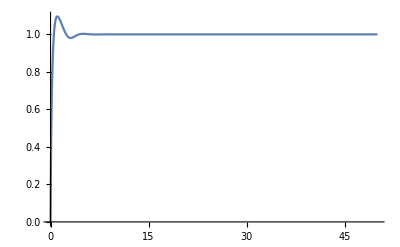

```mathematica
t0=0;
t1=50;
pim=StateSpaceModel[TransferFunctionModel[{{5+10/s}},s]];
nlm=NonlinearStateSpaceModel[{{0},{2 u^2}},x1,u];
forward=SystemsModelSeriesConnect[pim,nlm];
forward2=SystemsModelSeriesConnect[forward,TransferFunctionModel[{{1/(1+8s)}},s]];
closed=SystemsModelFeedbackConnect[forward2,TransferFunctionModel[{{1}},s]];
OutputResponse[closed,UnitStep[t],{t,t0,t1}];
Plot[%,{t,t0,t1},PlotRange->{All,{0,All}}]
```

```mathematica
pim=TransferFunctionModel[{{(1+1/(s+2))}},s];
pim2=TransferFunctionModel[{{SystemsModelDelay[10](1+1/s)}},s];
StateSpaceModel[pim];
fb=SystemsModelFeedbackConnect[pim];
pfb=SystemsModelFeedbackConnect[pim,"Positive"];
dfb=SystemsModelFeedbackConnect[pim2](*, TransferFunctionModel[{{SystemsModelDelay[.1]}},s]];*)
(*f=1;
t1=10;
drive=Sin[f t];
resp=OutputResponse[dfb,drive,{t,0,t1/f}];
Plot[{drive,resp},{t,0,t1/f},PlotLegends->"Expressions"]*)
```

((1+s) 10)/(s+(1+s) 10)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s111$CellContext`s1FalseFalseFalseAutomaticNoneAutomatic

```mathematica
pim2//Chop
```

(1. 0.1+s 0.1)/sTransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s111.$CellContext`s1FalseFalseFalseAutomaticNoneAutomatic

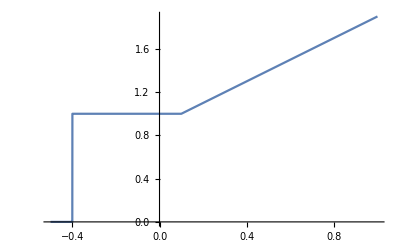

```mathematica
OutputResponse[pim2,UnitStep[0.0],{t,-.5,1}];
Plot[%,{t,-.5,1},PlotRange->All]
```

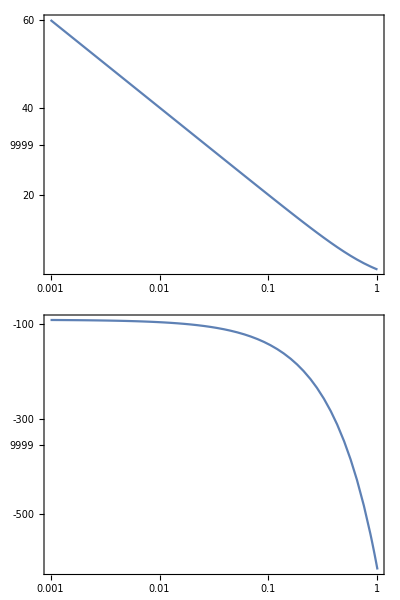

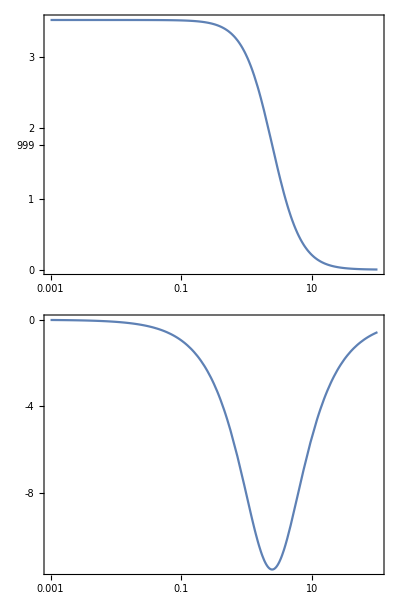

```mathematica
BodePlot[pim2,{.001,1},PlotRange->All]
BodePlot[pim,{.001,100},PlotRange->All]
```

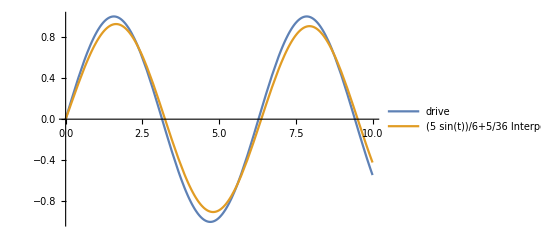

```mathematica
f=1;
t1=10;
drive=Sin[f t];
resp=OutputResponse[fb,drive,{t,0,t1/f}];
Plot[{drive,resp},{t,0,t1/f},PlotLegends->"Expressions"]
```

```mathematica
TransferFunctionModel[{{SystemsModelDelay[1]}},s]
```

1TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11111FalseFalseFalseAutomaticNoneAutomatic

((1+5 s) 5)/sTransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s111$CellContext`s1FalseFalseFalseAutomaticNoneAutomatic

0155 5StateSpaceModelFalseFalseFalseFalse$CellContext`stname1Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1111FalseFalseFalseAutomaticNoneAutomatic

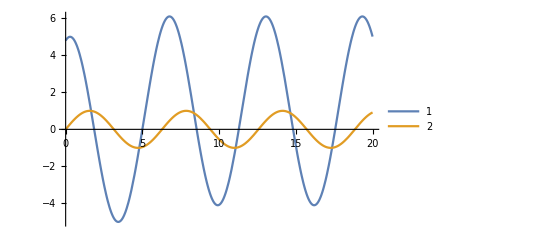

```mathematica
t1=20;
f=1;
drive=Sin[f t];
pim=TransferFunctionModel[{{SystemsModelDelay[5](5+1/s)}},s]
StateSpaceModel[pim]
(*ff=SystemsModelSeriesConnect[pim,TransferFunctionModel[{{SystemsModelDelay[5]}},s]]*)
(*ff2=SystemsModelFeedbackConnect[pim,TransferFunctionModel[{{1}},s]]*)
OutputResponse[pim,drive,{t,t0,t1}];
Plot[{%,drive},{t,0,t1/f},PlotRange->All,PlotLegends-> True]
```

```mathematica
ff2=SystemsModelFeedbackConnect[ff,TransferFunctionModel[{{1}},s]]
```

10-1-5 1100-1-1-5 1115 10StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseTrueAutomaticNoneAutomatic

```mathematica
TransferFunctionModel[ff2,s]
```

(ⅇ^-s+5 ⅇ^-s s)/(ⅇ^-s+s+5 ⅇ^-s s)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11EE1FalseFalseFalseAutomaticNoneAutomatic

```mathematica
10-1-5 1100-1-1-5 1115 10StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseTrueAutomaticNoneAutomatic
```

```mathematica
TransferFunctionModel[{{s/(1+s)}},s]
```

s/(1+s)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11$CellContext`s11FalseFalseFalseAutomaticNoneAutomatic

0151StateSpaceModelFalseFalseFalseFalse$CellContext`stname1Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1111FalseFalseFalseAutomaticNoneAutomatic

{1/50 (1+10 UnitStep[t]+10 InterpolatingFunction[{{0., 5.}}, <>][t]-√(1+20 UnitStep[t]+20 InterpolatingFunction[{{0., 5.}}, <>][t]))}

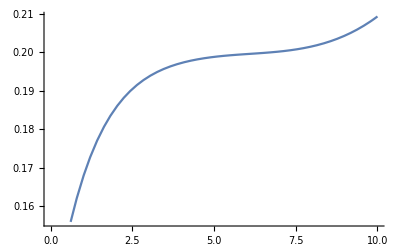

```mathematica
pim
```

0u^2x1 1111NoneNoneFalseFalseFalse{u}Automatic

0000StateSpaceModelFalseFalseFalseFalse$CellContext`stname1Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1111FalseFalseFalseAutomaticNone,{{x1,0}},{{u,0}}

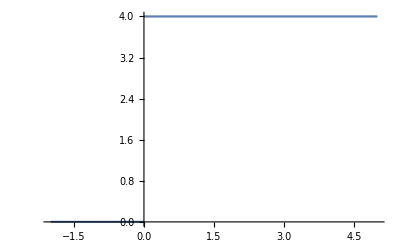

```mathematica
nlm=NonlinearStateSpaceModel[{{0},{u^2}},x1,u]
StateSpaceModel[nlm]
OutputResponse[nlm,2UnitStep[t],{t,-2,5}];
Plot[%,{t,-2,5}]
```

```mathematica
StateSpaceModel[TransferFunctionModel[{{1}},s]]
```

1StateSpaceModelFalseFalseFalseFalseControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1101FalseFalseFalseAutomaticNoneAutomatic